```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;m=1;a=1;V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefV[r].mx
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2[r].mx
```

```mathematica
evShifted=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"];
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[evShifted],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
```

```mathematica
energyVs2=EigenEnergy[Vs2[r],2m,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.55584,-0.184813,-0.0710039,-0.0373997,-0.0230491,-0.0156178,-0.0112775,-0.00852421,-0.00666874,-0.00535926,-0.00440078,-0.00367821,-0.00312002,-0.00267989,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1152]-u''[r$1152]/2==e$1151 u[r$1152],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.55584171106920168119852757804,-0.184812889024214410806649524407,-0.0710038755178704016686884013386,-0.0373996869555343989709252798785,-0.023049112944692063495906182412,-0.015617756515474989476410087635,-0.0112775314310717020703481622059,-0.00852420772379227836737303471501,-0.00666874384520550239888757310241,-0.0053592553736366795161081941027,-0.00440077846881845844414747306724,-0.00367820574069967249817645208039,-0.0031200212286267581328870061422,-0.0026798915499048504848387769317,-0.00232672805832252119388856670794,-0.00203904095001752525746398130219,-0.00180159046383176967700015456942,-0.00160332594166236277436199440248,-0.00143607629594663152513709746502,-0.0012936943396727817190393087774}

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/2m f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
AbsoluteTiming[efV=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],evShifted[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-1.3373203577743778777484998097 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.037407168809596011660801031892 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.011277794776154149484804536219 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0053592927931919616196373210951 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0044008009895061115267162099337 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.023050971823032012263856091426 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0085243331636150573081138113356 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.18643394332774011967873561071 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0036782199604481319905959313028 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.01561839001707619878572351763 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0066688098219347947110873233838 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.071057463765681416850087674062 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0031200305695982845354571364731 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0023267324899791593742692184066 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0018015927839557429811049162805 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0014360776057045943945272295712 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0026798978934000301370515335496 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0020390441226088289036420519245 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0016033276704600044466081691919 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.001293695346788560431501052664 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1466.25,{4.99684885394×10^-1372                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-4.0157001685×10^-477                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.71274×10^-271                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.7233×10^-179                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.48402×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.44109×10^-92                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.34474×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.90203×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.31977×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-4.51191×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.3994×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000127159                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],75.6287                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.32785×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],6.65569×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.41864×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0158851                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2475.86                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.13444×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-5.48857×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.55584171106920168119852757804 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.023049112944692063495906182412 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00666874384520550239888757310241 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0053592553736366795161081941027 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.015617756515474989476410087635 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.184812889024214410806649524407 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00440077846881845844414747306724 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112775314310717020703481622059 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0710038755178704016686884013386 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367820574069967249817645208039 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232672805832252119388856670794 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0031200212286267581328870061422 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160332594166236277436199440248 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203904095001752525746398130219 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0026798915499048504848387769317 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143607629594663152513709746502 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00180159046383176967700015456942 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0012936943396727817190393087774 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1377.72,{6.33092024525×10^-1484                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-8.51113405481×10^-475                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.27552×10^-271                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.82317×10^-179                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.51105×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.49005×10^-92                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.35357×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.91436×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.32143×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-4.51555×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.40016×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000127207                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],75.6493                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.32853×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],6.65718×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.41906×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0158872                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2476.13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.13454×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-5.48908×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDATA_δefVHQ.mx",efV];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2HQ.mx",efVs2];
```

```mathematica
<<D:\\Documents\\TestDATA_δefVHQ.mx;
<<D:\\Documents\\TestDATA_δefVs2HQ.mx;
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ψV=efV/(√(4π)r);
ψVs2=efVs2/(√(4π)r);
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]];
```

```mathematica
lap[δa[r],r]
```

(ⅇ^(-r^2/2) (-3+r^2))/(2 √2 π^(3/2))

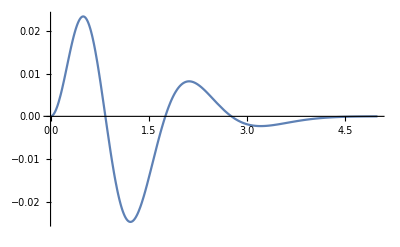

```mathematica
lap[Evaluate[ψVs2[[3]]lap[δa[r],r]],r] r^2;
Plot[%,{r,0,5},PlotRange->All]
```

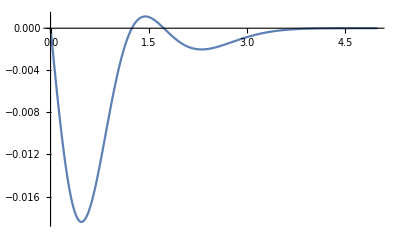

```mathematica
efVs2[[3]]Laplacian[δa[r],{r,θ,ϕ},"Spherical"];
Plot[%,{r,0,5},PlotRange->All]
```

```mathematica
NIntegrate[Laplacian[ψVs2[[3]]Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]
```

NIntegrate::precw: The precision of the argument function (r^2 (-(1.28383×10^-271 «1» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},«33»,{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},«14430»},{«1»}}}][r])/r^2+(1.28383×10^-271 ((«1»)/(«1»)-(«1»)/(«1»)) InterpolatingFunction[«1»][r])/r+(«24» («1») «1»[r])/r+(«1»)/r^3-(1.28383×10^-271 («1») «1»[r])/r^2+(6.41914×10^-272 («1») InterpolatingFunction[{{«95»,2000.}},«3»,{{{{«1»},{«1»},{«1»},{«1»},«43»,{«1»},{«1»},{«1»},«14430»},{«1»}}}][r])/r)) is less than WorkingPrecision (30.).

-0.0210196411179276697861632493689

```mathematica
Integration1st=NIntegrate[ψVs2[[#]]δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
Integration2nd=NIntegrate[ψVs2[[#]]Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
(*Integration3rd=NIntegrate[Laplacian[ψVs2[[#]]Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20*)
```

NIntegrate::precw: The precision of the argument function (1.13394530688×10^-1485 ⅇ^(«1») r InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«59556»},{NDSolve`LocalSeries,NDSolve`LocalSeries,NDSolve`LocalSeries,NDSolve`LocalSeries,«44»,NDSolve`LocalSeries,NDSolve`LocalSeries,«59556»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-1.52444828616×10^-476 ⅇ^(-r^2/2) r «1»[r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (4.07574×10^-273 ⅇ^(-r^2/2) r «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.0118215080565274633679129365671,-0.000230585731860807745873395025062,-0.000152021446010252996195563693726,-0.000100040641415856068698370303152,-0.0000712863696030750760308862733496,-0.0000538816240874524222514184383126,-0.000042497719274684537567399581257,-0.000034598832292035818358133435989,-0.0000288636620686676464991794115396,-0.000024548362142193563153062934233,-0.0000212070367745977352779312768087,-0.0000185583809728414742227297256982,-0.0000164172901155582930761584187285,-0.0000146575953572103198777768069555,-0.0000131906947864411964286091342299,-0.0000119527562533525786104601369586,-0.0000108967627026125258422191328273,-9.98740544461156432472928123163×10^-6,-9.1977119667846575336049372313×10^-6,-8.50676309962909235686696726864×10^-6}

NIntegrate::precw: The precision of the argument function (1.78591962832×10^-1484 r («1») InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«59556»},{NDSolve`LocalSeries,NDSolve`LocalSeries,NDSolve`LocalSeries,NDSolve`LocalSeries,«44»,NDSolve`LocalSeries,NDSolve`LocalSeries,«59556»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-2.40094658895×10^-475 r (-(3 «1»)/(«1»)+(«1»)/(«1»)) InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«20425»},{NDSolve`LocalSeries,NDSolve`LocalSeries,NDSolve`LocalSeries,«45»,NDSolve`LocalSeries,NDSolve`LocalSeries,«20425»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (6.41914×10^-272 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.019109801604801116473152969112,-0.00751625394405966676112456170495,-0.00332666171518680267941743036217,-0.00199746107718203008506929484231,-0.00137211050009413366435407115627,-0.00101813886963498533494819677817,-0.000794544978079991515182232400281,-0.000642559096551743960491777431853,-0.000533652914814112474478042949423,-0.000452442225908873803634595617196,-0.000389962525302614735754734004177,-0.000340668776092663919898929533787,-0.000300964132714077747273244781925,-0.000268423181666961222274932596027,-0.000241356739650851975400328478831,-0.000218555775466834125947621338372,-0.00019913440148578686319417128427,-0.00018243017060556508759089442466,-0.000167938816310640082250649685329,-0.000155270393152847711368196324367}

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ Integration1st[[n]]+η a^2 Integration2nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

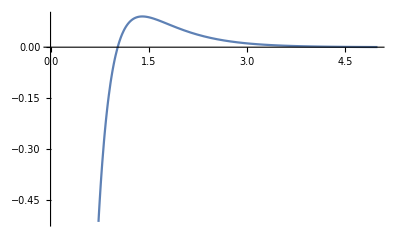

```mathematica
lap[efV[[1]]/(√(4π)r),r];
Plot[%,{r,0,5}]
```

```mathematica
γl={};ηl={};
```

```mathematica
Determine[0.1]
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000131906947864411964286091342299 γ-0.000241356739650851975400328478831 η)==-0.452637,4 π (-8.50676309962909235686696726864×10^-6 γ-0.000155270393152847711368196324367 η)==-0.29146}) is less than WorkingPrecision (30.).

{{0.1,1023.56686758620084256524449383},{0.1,93.2981609610062158830046367935}}

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γl={};ηl={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γl,γη[[1]]];
AppendTo[ηl,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
γl
ηl
```

```mathematica
γr=Interpolation[γl]
ηr=Interpolation[ηl]
```

InterpolatingFunction[{{0.01, 1.}}, <>]

InterpolatingFunction[{{0.01, 1.}}, <>]

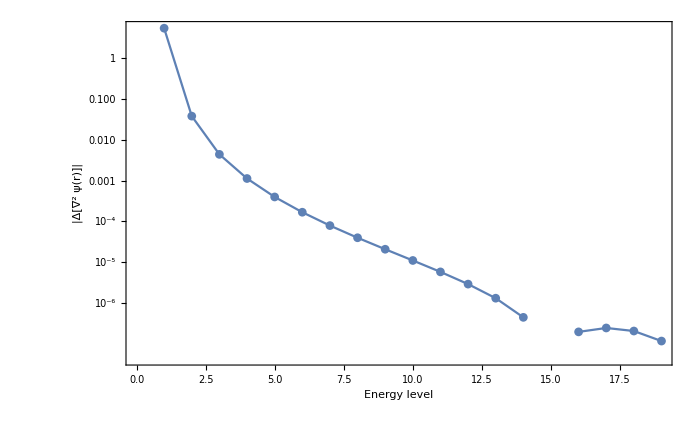

C:\Users\yingsheng\OneDrive\Documents\Test_6\psirlap1.eps

```mathematica
ListLogPlot[ReplacePart[Table[Mean[Table[Abs[(ψrfunlap[r][n]-lapV[[n]])/lapV[[n]]],{r,0.01,1,0.01}]],{n,1,20}],{{15},{20}}->0],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->700,FrameLabel->Reverse@{"|Δ[∇^2 ψ(r)]|","Energy level"},RotateLabel->True]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\psirlap1.eps",%]
```

```mathematica
lapV=Table[lap[efV[[n]]/(√(4π)r),r],{n,20}];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

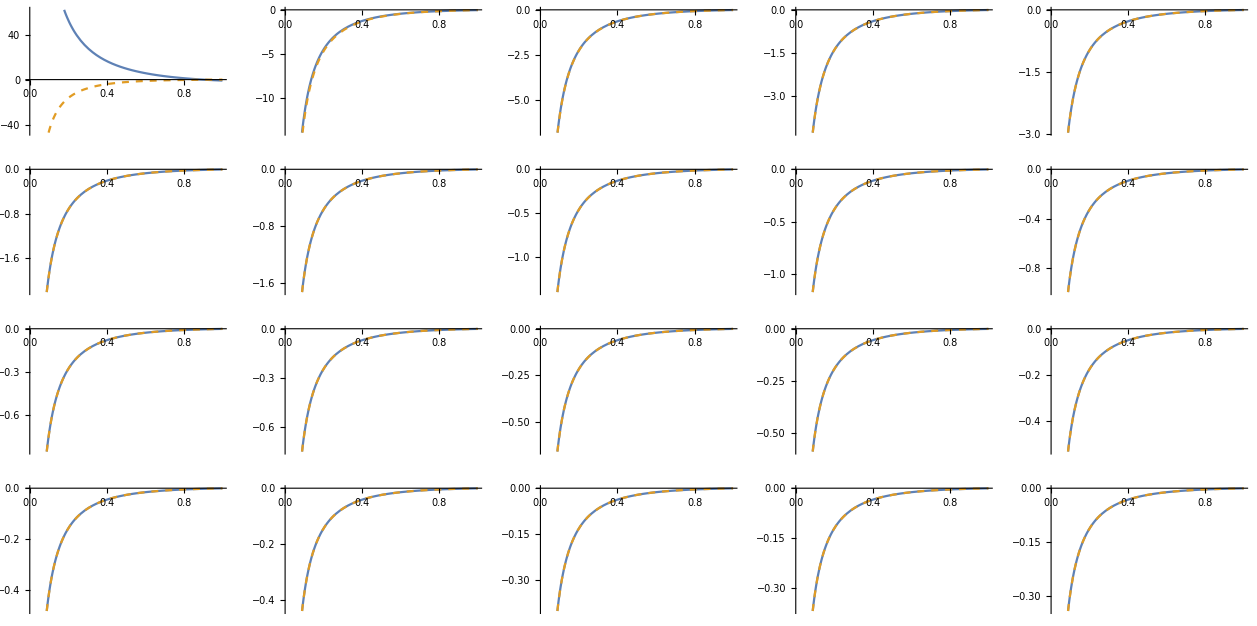

C:\Users\ASUS\OneDrive\Documents\Test_6\psirlap.eps

```mathematica
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],Evaluate@lap[efV[[n]]/(√(4π)r),r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psirlap.eps",%]
```